```mathematica
(*Para ejecutar este programa se tienen que ejecutar los programas: Golden section search y Kramers-Kronig_Dielectric_function*)
```

## Constantes

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
omega=Range[0,10,0.01];
```

```mathematica
h c/5
```

248.14

## Funciones generales

```mathematica
(*Función que devuelve la parte real y la imaginaria de la función dieléctrica a partir del índice de refracción*)
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
(*Función para encontrar los máximos alrededor de intervalos dados*)
ω0i[eps_,intervalos_]:=GoldenSearchMax[eps,##]&@@@intervalos;
(*Parte imaginaria de lorentziana*)
lorentzIm[ω_,ω0_,γ_]:=(γ ω)/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 5 lorentzianas*)
lorentzSumIm5[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5];
(*Definición de 6 lorentzianas*)
lorentzSumIm6[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_,A6_,ω06_,γ6_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+ A4 lorentzIm[ω,ω04,γ4]+ A5 lorentzIm[ω,ω05,γ5]+A6 lorentzIm[ω,ω06,γ6];
(*Definición de 4 lorentzianas*)
lorentzSumIm4[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:=A1 lorentzIm[ω,ω01,γ1]+A2 lorentzIm[ω,ω02,γ2]+A3 lorentzIm[ω,ω03,γ3]+A4 lorentzIm[ω,ω04,γ4];

(*Parte real de lorentziana*)
lorentzRe[A_,ω_,ω0_,γ_]:=1+(A *(ω0^2-ω^2))/((ω0^2-ω^2)^2+(γ ω)^2)
(*Definición de 5 lorentzianas*)
lorentzSumRe5[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_,A5_,ω05_,γ5_]:= lorentzRe[A1,ω,ω01,γ1]+lorentzRe[A2,ω,ω02,γ2]+ lorentzRe[A3,ω,ω03,γ3]+lorentzRe[A4,ω,ω04,γ4]+lorentzRe[A5,ω,ω05,γ5];
(*Definición de 4 lorentzianas*)
lorentzSumRe4[ω_,A1_,ω01_,γ1_,A2_,ω02_,γ2_,A3_,ω03_,γ3_,A4_,ω04_,γ4_]:= lorentzRe[A1,ω,ω01,γ1]+lorentzRe[A2,ω,ω02,γ2]+ lorentzRe[A3,ω,ω03,γ3]+lorentzRe[A4,ω,ω04,γ4];
```

## Concentración 28.7 g/dL

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm28=Interpolation[parteIm280,InterpolationOrder->1];
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]];
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];
(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1);
parteRe28[x_]:=parteRe[x,28.7];
```

SetDelayed::write: Tag InterpolatingFunction in InterpolatingFunction[{{1.1276,4.82414}},{5,7,0,{90},{4},0,0,0,0,Automatic,{},{},False},{{1.1276,1.13751,1.15527,1.17625,1.19802,1.21488,1.22929,1.24107,«36»,1.90877,1.93011,1.96675,2.00481,2.03633,2.06887,«40»}},«1»,{Automatic}][x_] is Protected.

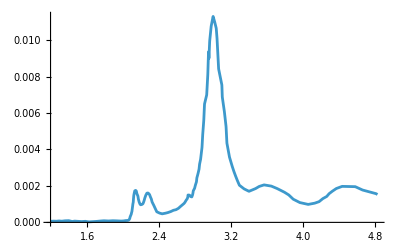

InterpolatingFunction::dmval: Input value {1.10008} lies outside the range of data in the interpolating function. Extrapolation will be used.

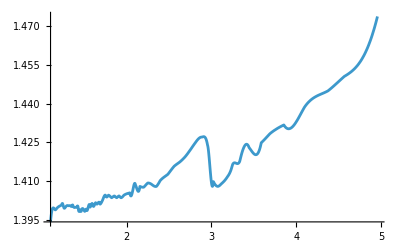

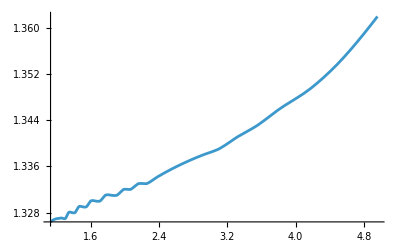

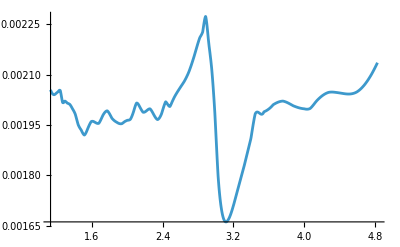

```mathematica
Plot[{parteIm28[x]},{x,1.19,4.83},PlotRange->All]
Plot[{parteRe28[x]},{x,1.1,4.96},PlotRange->All]
Plot[{h2o[x]},{x,1.13,4.96},PlotRange->All]
Plot[{beta[x]},{x,1.13,4.83},PlotRange->All]
```

```mathematica
h c/1150
```

1.07887

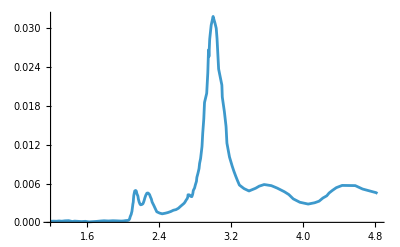

```mathematica
Plot[{epsIm[parteRe28,parteIm28,x]},{x,1.19,4.83},PlotRange->All]
```

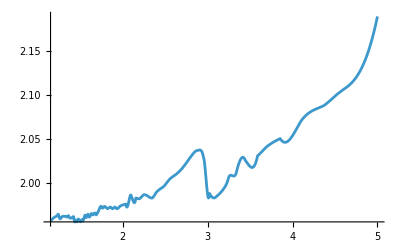

```mathematica
Plot[{epsRe[parteRe28,parteIm28,x]},{x,1.15,5},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos28={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};
eps28[x_]:=epsIm[parteRe28,parteIm28,x];
ω0i28=ω0i[eps28,intervalos28];
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin,xmax}={Min[datos2Im],Max[datos2Im]};
```

InterpolatingFunction::dmval: Input value {4.83} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.85} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {4.8263} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.8363} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.8463} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

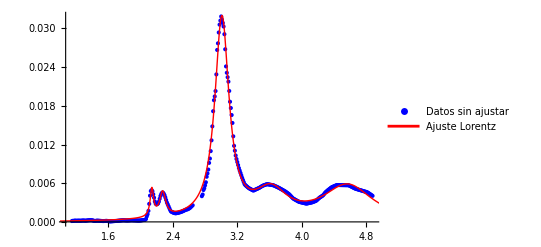

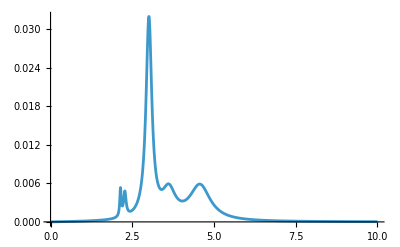

{A1→4.73×10^-4,ω01→2.14,γ1→5.15×10^-2,A2→7.85×10^-4,ω02→2.27,γ2→9.11×10^-2,A3→2.×10^-2,ω03→3.01,γ3→2.13×10^-1,A4→7.52×10^-3,ω04→3.63,γ4→4.88×10^-1,A5→1.92×10^-2,ω05→4.59,γ5→7.64×10^-1}

{0.000473117,2.1396,0.0515247,0.000784958,2.27347,0.0911428,0.0199706,3.01098,0.213223,0.00751609,3.62547,0.488187,0.0192421,4.58776,0.764428}

```mathematica
(*Datos para ajuste ignorando el pico pequeño faltante*)
eps28Data0=Table[{x,eps28[x]},{x,xmin,2.65,0.01}];
eps28Data1=Table[{x,eps28[x]},{x,2.76,xmax,0.01}];
eps28Data2=Join[eps28Data0,eps28Data1];
eps28Data=Table[{x,eps28[x]},{x,xmin,xmax,0.01}];
(* Ajustar con NonlinearModelFit*)
fit28=NonlinearModelFit[eps28Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i28[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i28[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i28[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0i28[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i28[[5]]},{γ5,0.1}},ω];
(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps28Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28[ω],{ω,0,10},PlotRange->All]
ScientificForm[fit28["BestFitParameters"],3]
fit28Values=Values[fit28["BestFitParameters"]]
```

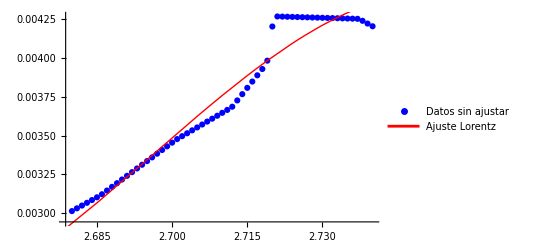

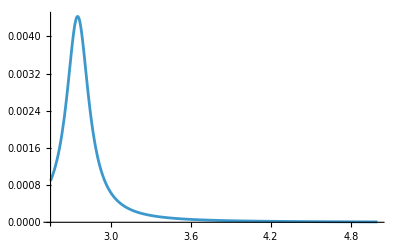

{A1→2.49×10^-3,ω01→2.75,γ1→2.04×10^-1}

{0.00248954,2.75493,0.204166}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps28Data3=Table[{x,eps28[x]},{x,2.68,2.74,0.001}];
fit281=NonlinearModelFit[eps28Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.7},{γ1,0.005}},ω];
Show[ListPlot[eps28Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit281[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit281[ω],{ω,2.55,5},PlotRange->All]
ScientificForm[fit281["BestFitParameters"],3]
fit281Values=Values[fit281["BestFitParameters"]]
```

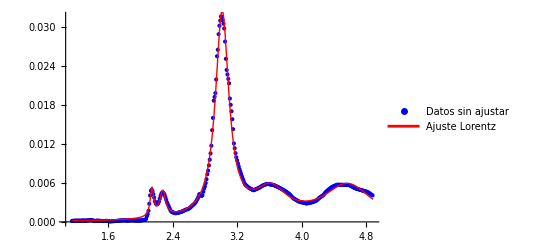

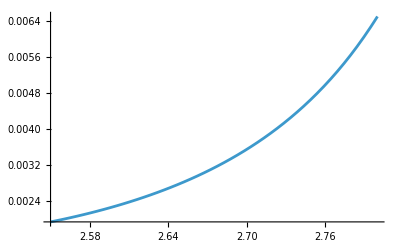

{A1→4.91×10^-4,ω01→2.14,γ1→5.29×10^-2,A2→7.79×10^-4,ω02→2.27,γ2→8.82×10^-2,A3→1.91×10^-2,ω03→3.01,γ3→2.02×10^-1,A4→7.86×10^-3,ω04→3.62,γ4→4.94×10^-1,A5→1.88×10^-2,ω05→4.58,γ5→7.43×10^-1,A6→2.16×10^-6,ω06→2.72,γ6→1.55×10^-1}

```mathematica
(*Datos para ajuste total*)
fit28tot=NonlinearModelFit[eps28Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],0.003>A6>0&&A1>0&&A2>0&&A3>0&&A4>0&&A5>0&&0.2>γ6>0.1&&2.77>ω06>2.66&&γ1>0&&2.3>ω02>2.2&&γ2>0&&γ3>0&&γ4>0&&γ5>0},{{A1,fit28Values[[1]]},{ω01,fit28Values[[2]]},{γ1,0.05},{A2,fit28Values[[4]]},{ω02,fit28Values[[5]]},{γ2,0.05},{A3,fit28Values[[7]]},{ω03,fit28Values[[8]]},{γ3,0.000005},{A4,fit28Values[[10]]},{ω04,fit28Values[[11]]},{γ4,0.0005},{A5,fit28Values[[13]]},{ω05,fit28Values[[14]]},{γ5,0.0005},{A6,fit281Values[[1]]},{ω06,fit281Values[[2]]},{γ6,fit281Values[[3]]}},ω,Weights->(If[2.67<#<2.75,50,1]&/@(eps28Data[[All,1]]))
];
Show[ListPlot[eps28Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit28tot[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit28tot[ω],{ω,2.55,2.8},PlotRange->All]
ScientificForm[fit28tot["BestFitParameters"],3]
```

```mathematica
parteIm028=Table[fit28tot[x],{x,0,10,0.01}];
parteReSSKK28=sskkrebook[omega,parteIm028,3.4,epsRe[parteRe28,parteIm28,3.4]];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.04967×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
hola=Interpolation[Transpose[{omega,parteReSSKK28}]];
hola2=hola/@datos2Im;
hola3=parteIm28/@datos2Im;
```

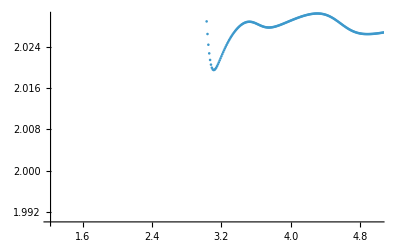

```mathematica
ListPlot[Transpose[{omega,parteReSSKK28}],PlotRange->{{1.23,5},{1.99,2.03}}]
```

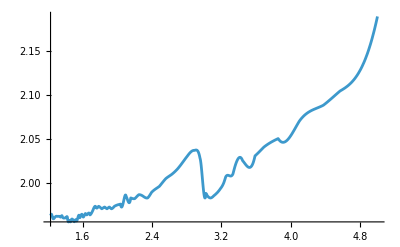

```mathematica
Plot[{epsRe[parteRe28,parteIm28,x]},{x,1.23,5},PlotRange->All]
```

```mathematica
h c/1050
```

1.18162

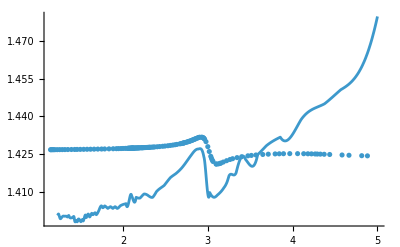

```mathematica
Show[ListPlot[Transpose[{datos2Im,Sqrt[hola2+hola3^2]}],PlotRange->All],
Plot[parteRe28[x],{x,1.23,5},PlotRange->All],PlotRange->All]
```

## Concentración 15.3 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuA=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\15.3_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA=Drop[datosuA,1];
datos1uA=Map[ToExpression,datos1uA,{2}];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im=h c/datos1uA[[All,1]];
(*Obtener la parte imaginaria del índice de refracción a partir del coeficiente de absorción*)
datos3im=((datos1uA[[All,2]]*10^(-6))/(4*Pi))*datos1uA[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm15=Interpolation[Transpose[{datos2im,datos3im}],InterpolationOrder->1];
parteRe15[x_]:=parteRe[x,15.3]
```

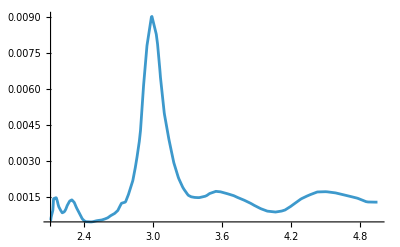

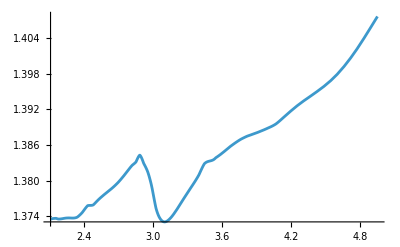

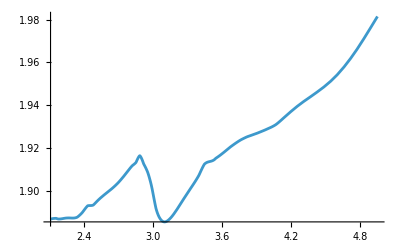

```mathematica
Plot[parteIm15[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe15[x],{x,2.11,4.95},PlotRange->All]
Plot[epsRe[parteRe15,parteIm15,x],{x,2.11,4.95},PlotRange->All]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos15={{2.13,2.15},{2.2,2.3},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps15[x_]:=epsIm[parteRe15,parteIm15,x];
ω0i15=ω0i[eps15,intervalos15];
```

InterpolatingFunction::dmval: Input value {1.1463} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.1563} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.1663} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{A1→3.48×10^-4,ω01→2.16,γ1→4.51×10^-2,A2→6.66×10^-4,ω02→2.29,γ2→9.1×10^-2,A3→1.52×10^-2,ω03→3.,γ3→2.09×10^-1,A4→6.22×10^-3,ω04→3.61,γ4→4.97×10^-1,A5→1.63×10^-2,ω05→4.58,γ5→7.7×10^-1}

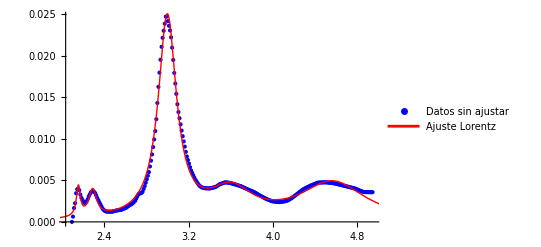

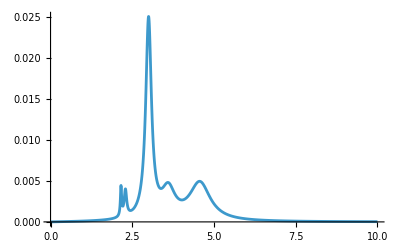

{0.000348046,2.15572,0.0451339,0.000666132,2.29124,0.090987,0.0152072,3.00076,0.208949,0.00621925,3.6094,0.497446,0.0162996,4.58385,0.769759}

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xmin15,xmax15}={Min[datos2im],Max[datos2im]};
(*Datos para ajuste*)
(*Datos para ajuste ignorando el pico pequeño faltante*)
eps15Data0=Table[{x,eps15[x]},{x,xmin,2.65,0.01}];
eps15Data1=Table[{x,eps15[x]},{x,2.76,xmax,0.01}];
eps15Data2=Join[eps15Data0,eps15Data1];
eps15Data=Table[{x,eps15[x]},{x,xmin15,xmax15,0.01}];

(* Ajustar ignorando el pico pequeño*)
fit15=NonlinearModelFit[eps15Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i15[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0i15[[2]]},{γ2,0.1},{A3,0.01},{ω03,ω0i15[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i15[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i15[[5]]},{γ5,0.1}},ω];
ScientificForm[fit15["BestFitParameters"],3]
(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps15Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit15[ω],{ω,xmin15-0.5,xmax15+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit15[ω],{ω,0,10},PlotRange->All]
fit15Values=Values[fit15["BestFitParameters"]]
```

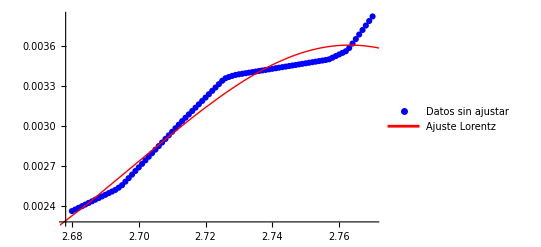

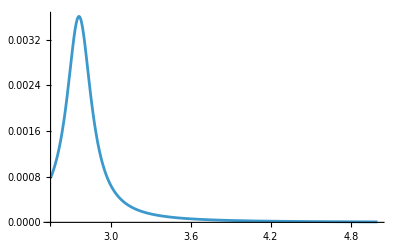

{A1→2.23×10^-3,ω01→2.77,γ1→2.23×10^-1}

{0.00222613,2.76539,0.22337}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps15Data3=Table[{x,eps15[x]},{x,2.68,2.77,0.001}];
fit151=NonlinearModelFit[eps15Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.005}},ω];
Show[ListPlot[eps15Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit151[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit151[ω],{ω,2.55,5},PlotRange->All]
ScientificForm[fit151["BestFitParameters"],3]
fit151Values=Values[fit151["BestFitParameters"]]
```

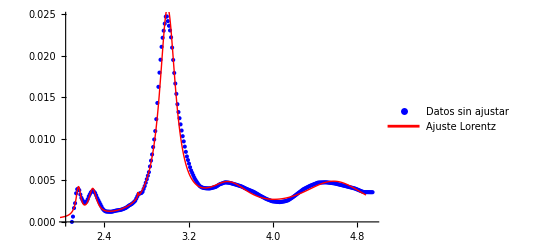

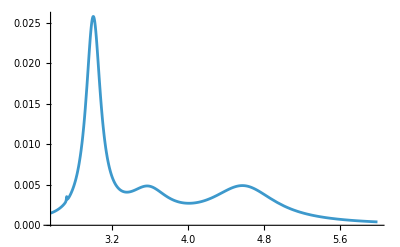

{A1→4.13×10^-4,ω01→2.16,γ1→5.61×10^-2,A2→6.64×10^-4,ω02→2.29,γ2→9.01×10^-2,A3→1.39×10^-2,ω03→3.,γ3→1.86×10^-1,A4→6.55×10^-3,ω04→3.59,γ4→5.14×10^-1,A5→1.76×10^-2,ω05→4.6,γ5→8.32×10^-1,A6→1.15×10^-5,ω06→2.72,γ6→7.83×10^-3}

```mathematica
(*Datos para ajuste total*)
fit15tot=NonlinearModelFit[eps15Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],0.002>A6>0&&0.2>γ6>0&&2.77>ω06>2.66},{{A1,fit15Values[[1]]},{ω01,fit15Values[[2]]},{γ1,fit15Values[[3]]},{A2,fit15Values[[4]]},{ω02,fit15Values[[5]]},{γ2,fit15Values[[6]]},{A3,fit15Values[[7]]},{ω03,fit15Values[[8]]},{γ3,fit15Values[[9]]},{A4,fit15Values[[10]]},{ω04,fit15Values[[11]]},{γ4,fit15Values[[12]]},{A5,fit15Values[[13]]},{ω05,fit15Values[[14]]},{γ5,fit15Values[[15]]},{A6,fit151Values[[1]]},{ω06,fit151Values[[2]]},{γ6,fit151Values[[3]]}},ω,Weights->(If[2.6<#<2.8,100,2]&/@(eps15Data[[All,1]]))
];
Show[ListPlot[eps15Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit15tot[ω],{ω,xmin,xmax},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit15tot[ω],{ω,2.55,6},PlotRange->All]
ScientificForm[fit15tot["BestFitParameters"],3]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 8.79827×10^-7.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

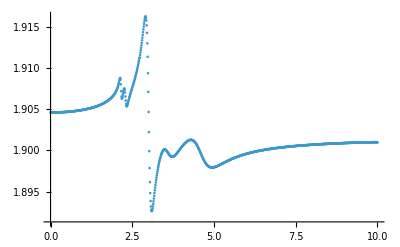

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm015=Table[fit15tot[x],{x,0,10,0.01}];
parteReSSKK15=sskkrebook[omega,parteIm015,2.89,epsRe[parteRe15,parteIm15,2.89]];
ListPlot[Transpose[{omega,parteReSSKK15}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,«29»,1.89868,1.89869,1.89869,1.89869,1.89869,1.8987,1.8987,1.8987,1.89871,1.89871,«951»}.

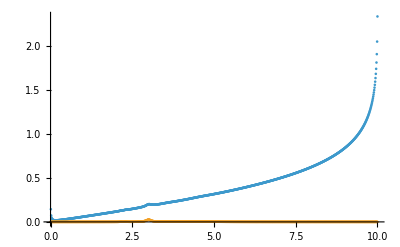

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK115=kkimbook[omega,parteReKK115];
ListPlot[{Transpose[{omega,parteImKK115}],Transpose[{omega,parteIm015}]},PlotRange->All]
```

```mathematica
eps15KK=selfconsbook[omega,parteReKK115,parteIm015,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,1.89864,«29»,1.89868,1.89869,1.89869,1.89869,1.89869,1.8987,1.8987,1.8987,1.89871,1.89871,«951»}.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

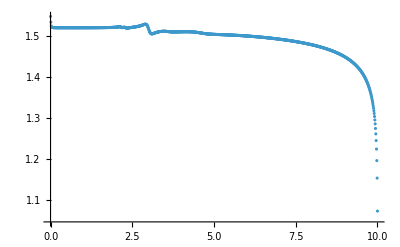

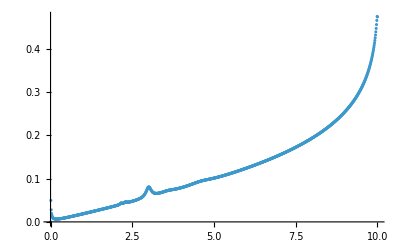

```mathematica
ListPlot[{Transpose[{omega,eps15KK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps15KK[[2]]}]},PlotRange->All]
```

## Concentración 30.6 g/dL

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
```

```mathematica
datosuA30=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA30=Drop[datosuA30,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im30=h c/datos1uA30[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteIm30=Interpolation[Transpose[{datos2im30,datos3im30}],InterpolationOrder->1];
parteRe30[x_]:=parteRe[x,30.6]
```

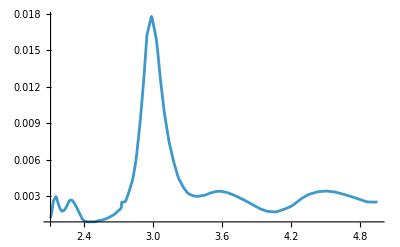

```mathematica
Plot[parteIm30[x],{x,2.11,4.95},PlotRange->All]
```

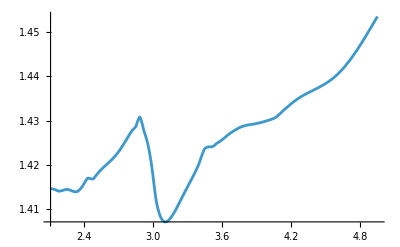

```mathematica
Plot[parteRe30[x],{x,2.11,4.95}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalos30={{2,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
eps30[x_]:=epsIm[parteRe30,parteIm30,x];
ω0i30=ω0i[eps30,intervalos30];
```

InterpolatingFunction::dmval: Input value {2.0382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.0618} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.07639} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

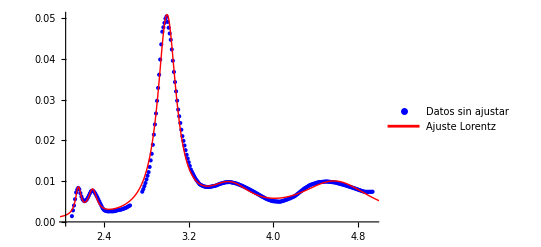

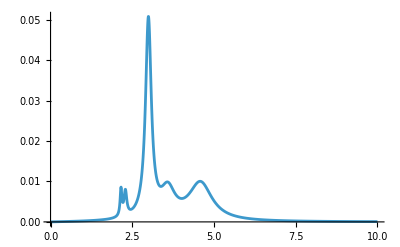

{0.000926901,2.15527,0.0647563,0.00141474,2.29027,0.101299,0.0312312,2.99569,0.212613,0.0131123,3.59669,0.528241,0.0370142,4.60619,0.858324}

{A1→9.27×10^-4,ω01→2.16,γ1→6.48×10^-2,A2→1.41×10^-3,ω02→2.29,γ2→1.01×10^-1,A3→3.12×10^-2,ω03→3.,γ3→2.13×10^-1,A4→1.31×10^-2,ω04→3.6,γ4→5.28×10^-1,A5→3.7×10^-2,ω05→4.61,γ5→8.58×10^-1}

```mathematica
(* Ajustar ignorando el pico pequeño*)
{xmin30,xmax30}={Min[datos2im30],Max[datos2im30]};
eps30Data0=Table[{x,eps30[x]},{x,xmin30,2.65,0.01}];
eps30Data1=Table[{x,eps30[x]},{x,2.76,xmax30,0.01}];
eps30Data2=Join[eps30Data0,eps30Data1];
eps30Data=Table[{x,eps30[x]},{x,xmin30,xmax30,0.01}];

(* Ajustar con NonlinearModelFit*)
fit30=NonlinearModelFit[eps30Data2,lorentzSumIm5[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5],{{A1,0.01},{ω01,ω0i30[[1]]},{γ1,0.01},{A2,0.01},{ω02,ω0i30[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0i30[[3]]},{γ3,0.1},{A4,0.01},{ω04,ω0i30[[4]]},{γ4,0.1},{A5,0.01},{ω05,ω0i30[[5]]},{γ5,0.1}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[eps30Data2,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit30[ω],{ω,xmin-0.5,xmax+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit30[ω],{ω,0,10},PlotRange->All]
fit30Values=Values[fit30["BestFitParameters"]]
ScientificForm[fit30["BestFitParameters"],3]
```

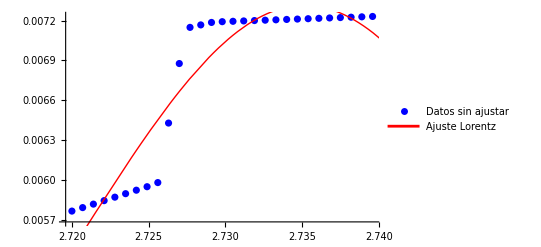

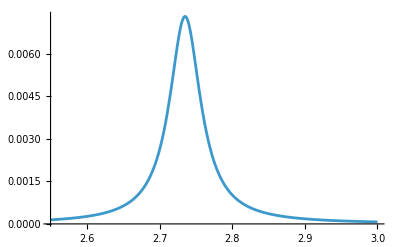

{A1→1.05×10^-3,ω01→2.74,γ1→5.23×10^-2}

{0.00104713,2.73529,0.0523398}

```mathematica
(*Datos para ajuste del pico pequeño*)
eps30Data3=Table[{x,eps30[x]},{x,2.72,2.74,0.0007}];
fit301=NonlinearModelFit[eps30Data3,A1*lorentzIm[ω,ω01,γ1],{{A1,0.0001},{ω01,2.75},{γ1,0.005}},ω];
Show[ListPlot[eps30Data3,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit301[ω],{ω,2.55,3.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fit301[ω],{ω,2.55,3},PlotRange->All]
ScientificForm[fit301["BestFitParameters"],3]
fit301Values=Values[fit301["BestFitParameters"]]
```

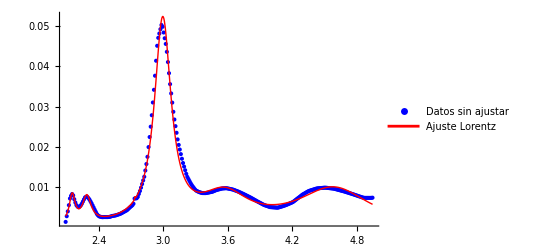

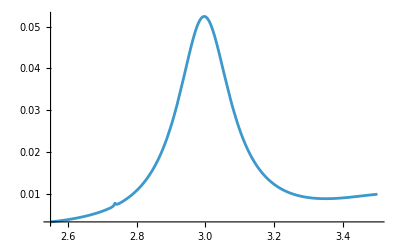

{A1→9.67×10^-4,ω01→2.16,γ1→6.58×10^-2,A2→1.43×10^-3,ω02→2.29,γ2→9.76×10^-2,A3→2.83×10^-2,ω03→3.,γ3→1.87×10^-1,A4→1.45×10^-2,ω04→3.58,γ4→5.48×10^-1,A5→3.61×10^-2,ω05→4.6,γ5→8.3×10^-1,A6→1.02×10^-5,ω06→2.74,γ6→6.14×10^-3}

```mathematica
(*Datos para ajuste total*)
fit30tot=NonlinearModelFit[eps30Data,{lorentzSumIm6[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4,A5,ω05,γ5,A6,ω06,γ6],A4>0&&A1>0&&A2>0&&A3>0&&A5>0&&γ1>0&&γ2>0&&γ3>0&&γ4>0&&γ5>0&&0.0001>A6>0.00001&&0.008>γ6>0.006&&2.76>ω06>2.72},{{A1,fit30Values[[1]]},{ω01,fit30Values[[2]]},{γ1,fit30Values[[3]]},{A2,fit30Values[[4]]},{ω02,fit30Values[[5]]},{γ2,fit30Values[[6]]},{A3,fit30Values[[7]]},{ω03,fit30Values[[8]]},{γ3,fit30Values[[9]]},{A4,fit30Values[[10]]},{ω04,fit30Values[[11]]},{γ4,fit30Values[[12]]},{A5,fit30Values[[13]]},{ω05,fit30Values[[14]]},{γ5,fit30Values[[15]]},{A6,fit301Values[[1]]},{ω06,fit301Values[[2]]},{γ6,fit301Values[[3]]}},ω,Weights->(If[2.72<#<2.8,70,2]&/@(eps30Data[[All,1]]))
];
Show[ListPlot[eps30Data,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fit30tot[ω],{ω,xmin30,xmax30},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All],PlotRange->All]
Plot[fit30tot[ω],{ω,2.55,3.5},PlotRange->All]
ScientificForm[fit30tot["BestFitParameters"],3]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.88751×10^-6.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

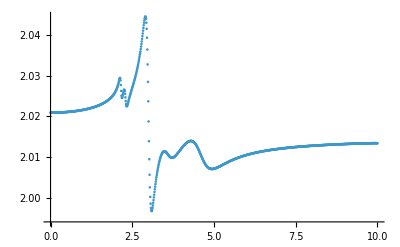

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm030=Table[fit30tot[x],{x,0,10,0.01}];
parteReSSKK30=sskkrebook[omega,parteIm030,2.9,epsRe[parteRe30,parteIm30,2.9]];
ListPlot[Transpose[{omega,parteReSSKK30}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,«29»,2.01127,2.01127,2.01128,2.01128,2.01129,2.01129,2.0113,2.01131,2.01131,2.01132,«951»}.

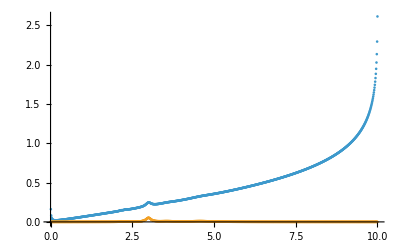

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK130=kkimbook[omega,parteReKK130];
ListPlot[{Transpose[{omega,parteImKK130}],Transpose[{omega,parteIm030}]},PlotRange->All]
```

```mathematica
eps30KK=selfconsbook[omega,parteReKK130,parteIm030,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,2.01117,«29»,2.01127,2.01127,2.01128,2.01128,2.01129,2.01129,2.0113,2.01131,2.01131,2.01132,«951»}.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

$Aborted

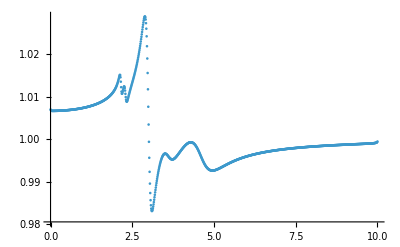

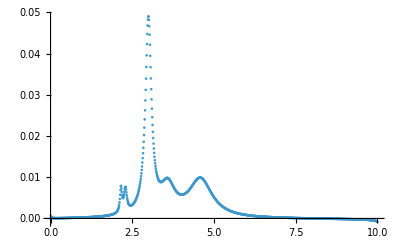

```mathematica
ListPlot[{Transpose[{omega,eps30KK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,eps30KK[[2]]}]},PlotRange->All]
```

## Comparación entre concentraciones

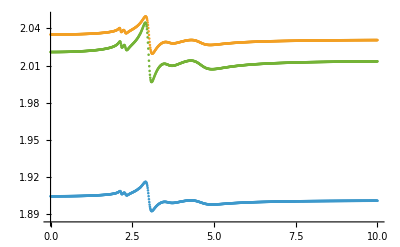

```mathematica
ListPlot[{Transpose[{omega,parteReSSKK15}],Transpose[{omega,parteReSSKK28}],Transpose[{omega,parteReSSKK30}]},PlotRange->All]
```

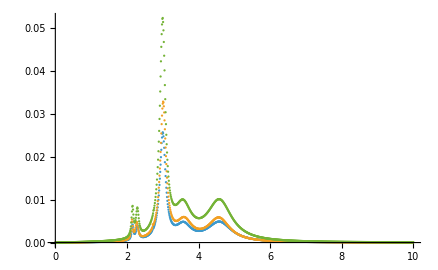

```mathematica
ListPlot[{Transpose[{omega,parteIm015}],Transpose[{omega,parteIm028}],Transpose[{omega,parteIm030}]},PlotRange->All]
```

## Plasma

```mathematica
(*Se van a importar los datos de la parte real del índice de refracción y del coeficiente de absorción*)
datosuAPlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\uA_ImN_Plasma.csv"];
datosRePlasma=Import["C:\\Users\\Nanoplasmonics\\Documents\\Tesis\\Refractive index\\ReN_Plasma.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uAPlasma=Drop[datosuAPlasma,1];
datos1RePlasma=Drop[datosRePlasma,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2imPlasma=h c/datos1uAPlasma[[All,1]];
datos2rePlasma=h c/datos1RePlasma[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3imPlasma=datos1uAPlasma[[All,2]]*10^(-6)*datos1uAPlasma[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteImPlasma=Interpolation[Transpose[{datos2imPlasma,datos3imPlasma}],InterpolationOrder->1];
parteRePlasma=Interpolation[Transpose[{datos2rePlasma,datos1RePlasma[[All,2]]}]]
```

InterpolatingFunction[…]

```mathematica
resampledA={#,parteRePlasma[#]}&/@(datos2imPlasma);
```

InterpolatingFunction::dmval: Input value {3.52512} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.47681} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.40263} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
epsPlasma2=2*resampledA[[All,2]]*datos3imPlasma;
epsPlasma3=Transpose[{datos2imPlasma,epsPlasma2}];
```

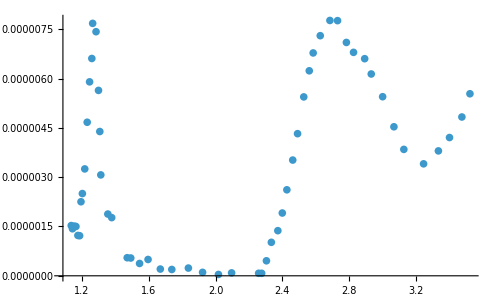

```mathematica
ListPlot[Transpose[{datos2imPlasma,epsPlasma2}]]
```

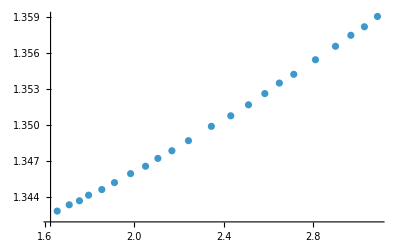

```mathematica
ListPlot[Transpose[{datos2rePlasma,datos1RePlasma[[All,2]]}]]
```

InterpolatingFunction::dmval: Input value {1.10004} lies outside the range of data in the interpolating function. Extrapolation will be used.

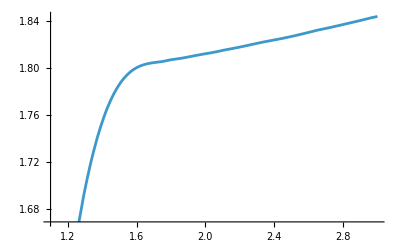

```mathematica
Plot[(parteRePlasma[x])^2,{x,1.1,3}]
```

```mathematica
(*Intervalos de búsqueda de los máximos*)
intervalosPlasma={{1.2,1.3},{2.57,2.8},{2.8,2.9},{3.4,3.5}};
epsPlasma[x_]:=epsIm[parteRePlasma,parteImPlasma,x];
ω0iPlasma=ω0i[epsPlasma,intervalosPlasma];
```

InterpolatingFunction::dmval: Input value {1.2382} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.2618} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.27639} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.13472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.14472} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.15472} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

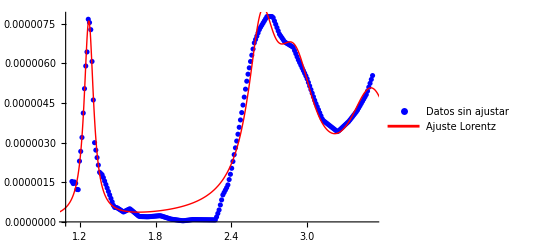

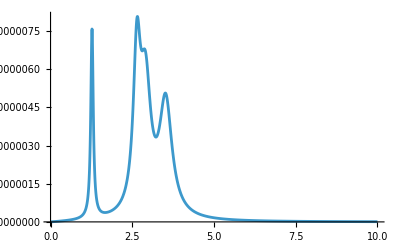

```mathematica
(*Ajuste de la parte imaginaria con lorentzianas*)
{xminPlasma,xmaxPlasma}={Min[datos2imPlasma],Max[datos2imPlasma]};
(*Datos para ajuste*)
epsPlasmaData=Table[{x,epsPlasma[x]},{x,xminPlasma,xmaxPlasma,0.01}];
(* Ajustar con NonlinearModelFit*)
fitPlasma=NonlinearModelFit[epsPlasmaData,lorentzSum4Im[ω,A1,ω01,γ1,A2,ω02,γ2,A3,ω03,γ3,A4,ω04,γ4],{{A1,0.01},{ω01,ω0iPlasma[[1]]},{γ1,0.05},{A2,0.01},{ω02,ω0iPlasma[[2]]},{γ2,0.05},{A3,0.01},{ω03,ω0iPlasma[[3]]},{γ3,0.05},{A4,0.01},{ω04,ω0iPlasma[[4]]},{γ4,0.05}},ω];

(*Grafica datos originales y ajuste con 5 Lorentzianas*)
Show[ListPlot[epsPlasmaData,PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],Plot[fitPlasma[ω],{ω,xminPlasma-0.5,xmaxPlasma+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]
Plot[fitPlasma[ω],{ω,0,10},PlotRange->All]
```

```mathematica
ScientificForm[fitPlasma["BestFitParameters"],3]
```

{A1→8.66×10^-7,ω01→1.27,γ1→9.15×10^-2,A2→4.08×10^-6,ω02→2.65,γ2→2.61×10^-1,A3→5.69×10^-6,ω03→2.91,γ3→3.93×10^-1,A4→7.36×10^-6,ω04→3.53,γ4→4.66×10^-1}

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object 0..

Set::setraw: Cannot assign to raw object 1.05547×10^-9.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

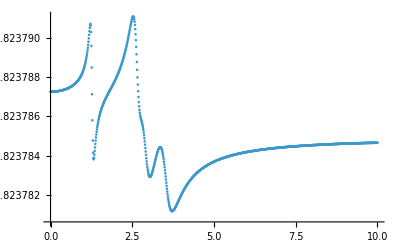

```mathematica
(*Obtención de la parte real a partir de la parte imaginaria con KK*)
parteIm0Plasma=Table[fitPlasma[x],{x,0,10,0.01}];
parteReKK1Plasma=sskkrebook[omega,parteIm0Plasma,2.4,epsRe[parteRePlasma,parteImPlasma,2.4]];
ListPlot[Transpose[{omega,parteReKK1Plasma}],PlotRange->All]
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«29»,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«951»}.

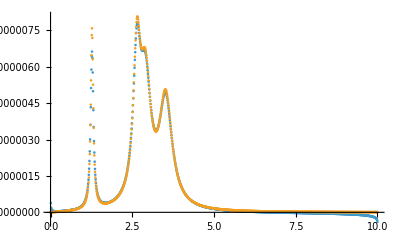

```mathematica
(*Obtención de la parte imaginaria a partir de la real obtenida con KK*)
parteImKK1Plasma=kkimbook[omega,parteReKK1Plasma];
ListPlot[{Transpose[{omega,parteImKK1Plasma}],Transpose[{omega,parteIm0Plasma}]},PlotRange->All]
```

```mathematica
epsPlasmaKK=selfconsbook[omega,parteReKK1Plasma,parteIm0Plasma,10,0.5];
```

Set::setraw: Cannot assign to raw object {0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,«951»}.

Set::setraw: Cannot assign to raw object {1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«29»,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«951»}.

Set::setraw: Cannot assign to raw object 0..

General::stop: Further output of Set::setraw will be suppressed during this calculation.

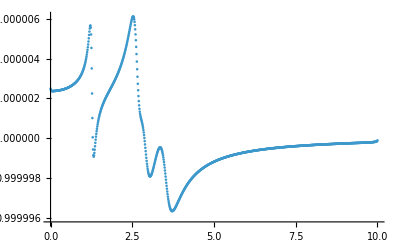

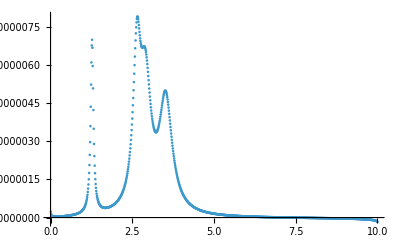

```mathematica
ListPlot[{Transpose[{omega,epsPlasmaKK[[1]]}]},PlotRange->All]
ListPlot[{Transpose[{omega,epsPlasmaKK[[2]]}]},PlotRange->All]
```